## Matrix Element calculation (including time evolution)

```mathematica
Clear[ω,ωt,t]
```

```mathematica
L =3.*10^-7; Lstep =1.*10^-8; LN = 2.*L/Lstep + 1.;nmax = 15.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
Uprop[x_,xt_,t_,ωt_]:= ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)]
deltak = 2 Pi/(455 10^-9)//N
ψ[x_, n_, ω_]:= 1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]
ψf[xt_, nt_, ωt_]:= 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]
```

1.38092×10^7

```mathematica
omega[3]
omega[4]
```

```mathematica
2*52564.18722654877
```

105128.

```mathematica
2 Pi/(30 10^-6)//N
```

209440.

```mathematica
2*96487.56959133178
```

192975.

```mathematica
omega[3],omega[5], (1/g35)
```

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.  + 0.\ ⅈ encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

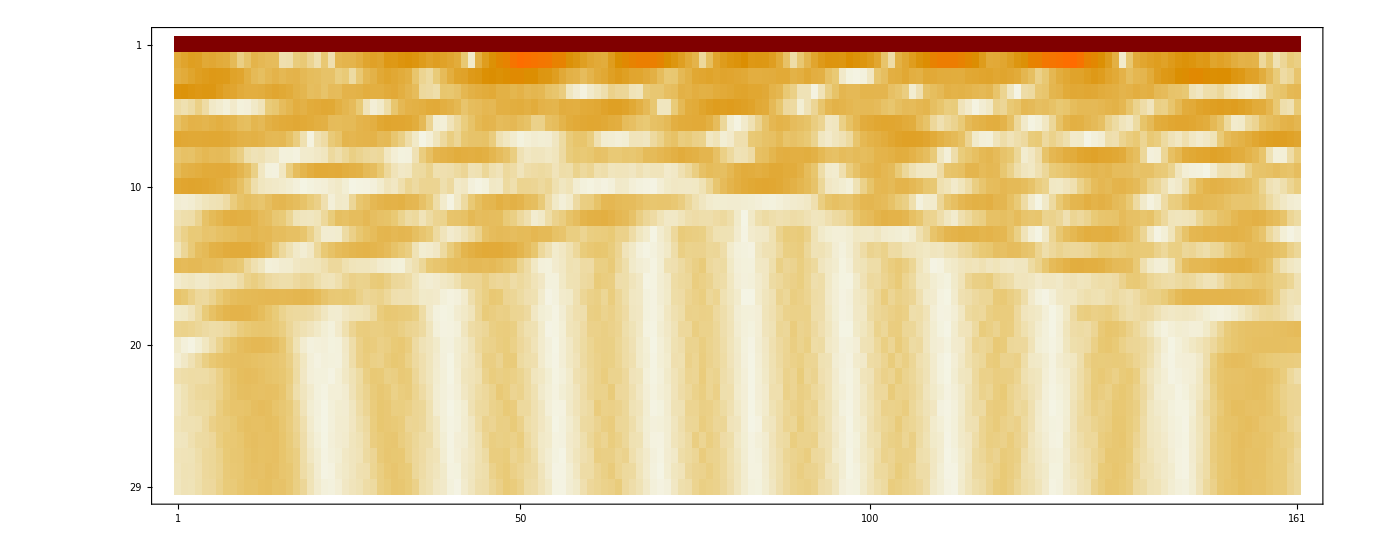

```mathematica
L =0.4*10^-6; Lstep =0.05*10^-7; LN = 2*L/Lstep + 1;
psi[t_, xt_,ω_,ωt_, n_] :=  Lstep*Sum[ψ[x, n, ω]*  Uprop[x,xt,t,ωt],{x,-L,L,Lstep}]
Monitor[evolmat = Table[Abs[psi[t, xt,omega[3],omega[5]/2, 9]]^2,{t,0,2000 10^-9, 70 10^-9},{xt, -L, L, Lstep}];,{(t/(400 10^-9))//N,(xt/L)}]
MatrixPlot[evolmat]
```

```mathematica
nmax = 19.;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.8*10^-6; Lstep =0.2*10^-7; LN = 2*L/Lstep + 1;
deltak = 2 Pi/(455 10^-9)//N;
```

```mathematica
UPn[ω_, ωt_,n_, nt_, t_] := Lstep^2 *Sum[ 1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]
```

$Aborted

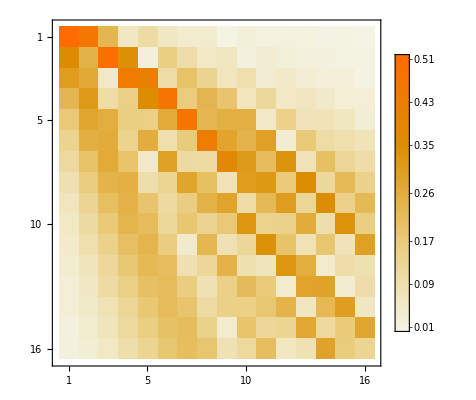

```mathematica
Monitor[ω = omega[1]; ωt=omega[2]; t= 10^-5;uma = Table[Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}];,{n,nt}]
MatrixPlot[uma, PlotLegends -> True]
```

## Calculate matrix elements for all segments (Are the decay times of the order of typical ωt? Here: assumed much smaller)

```mathematica
(*from LambDickeParams_Singe.py @532nm and @10**7 lattice beam intensity *)
(*levels=["6s 2 S 1/2","7p 2 P ?3/2","7s 2 S 1/2","6p 2 P ?1/2","6p 2 P ?3/2","5d 2 D 3/2","5d 2 D 5/2"]*)
(*decays=[l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34]*)
omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};
etas = {0.697646827167697,0.14448683087878345,0.17095247621856766,0.35533728030290285,0.10383570605450117,0.3729352538139725,0.06952852571696208,0.07198024772090308,0.19467123685222815,0.21390857630773225,0.23003214721947357};
l21=455.5*10^-9;
l23=2931.8*10^-9;
l35=1469.9*10^-9;
l41=894.3*10^-9;
l64=3011.1*10^-9;
l51=852.1*10^-9;
l65=3614.1*10^-9;
l75=3491*10^-9;
l27=1360.6*10^-9;
l26=1342.8*10^-9;
l34=1359.2*10^-9;
decays={l21,l23,l35,l41,l64,l51,l65,l75,l27,l26,l34};
g23=4.05*10^6;
g34=6.23*10^6;
g35=11.4*10^6;
g41=28.6*10^6;
g26=0.13*10^6;
g27=1.10*10^6;
g75=0.78*10^6;
g65=0.11*10^6;
g51=32.8*10^6;
g64=0.91*10^6;
g21=1.84*10^6;
gammas={g21,g23,g35,g41,g64,g51,g65,g75,g27,g26,g34};
omega[n_]:= omegas[[n]]/1.01
eta[n_]:= etas[[n]]
nmax = 20;c = 2.997 10^8;hbar = 1.0545718×10^-34;m = 132.90 * 1.660539 10^-27 ; 
L =0.6*10^-6; Lstep =0.09*10^-7; LN = 2*L/Lstep + 1;deltak = 2 Pi/(455 10^-9)//N;
ωg = omega[1];
```

```mathematica
Clear[t]
```

```mathematica
(*IntU[ω_,ωt_,τ_]:= Monitor[tstart = τ/10;tstop = 3*τ //N; tstep =(tstop/5)//N;*)
IntU[ω_,ωt_,τ_]:= Monitor[tstart =2.5 10^6;tstop = 2.5 10^-6 //N; tstep =τ//N; t = tstart;uma = Table[
Lstep^2 *ParallelSum[1/Sqrt[2^nt nt!]((m ωg)/(Pi hbar))^(1/4)Exp[(-m ωg xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωg)/hbar]xt]*1/Sqrt[2^n n!]((m ωg)/(Pi hbar))^(1/4)Exp[(-m ωg x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ωg)/hbar]x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}],{n,0.,nmax},{nt,0.,nmax}] ,{n,nt,t//N}];(*Abs[Lstep^2 *Sum[1/Sqrt[2^nt nt!]((m ωt)/(Pi hbar))^(1/4)Exp[(-m ωt xt^2)/(2 hbar)]HermiteH[nt, Sqrt[(m ωt)/hbar]xt]*1/Sqrt[2^n n!]((m ω)/(Pi hbar))^(1/4)Exp[(-m ω x^2)/(2 hbar)]HermiteH[n, Sqrt[(m ω)/hbar]x]*Exp[ⅈ  deltak x]* ((m ωt)/(2 Pi ⅈ hbar Sin[ ωt  t]))^(1/2)Exp[(ⅈ m ωt)/(2 hbar Sin[ωt t])((x^2+xt^2) Cos[ωt t ] - 2 x xt)],{x,-L,L,Lstep}, {xt,-L,L,Lstep}]]^2,{n,0.,nmax},{nt,0.,nmax}] Exp[-t/τ]/τ,{t,tstart, tstop, tstep}],{n,nt,t//N}]*)
Drw[n_,nt_, η_, θ_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[θ])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[θ])^2]Exp[-(η  Cos[θ])^2/2];
IntDr[η_]:= Table[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  Cos[Pi/4])^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  Cos[Pi/4])^2]Exp[-(η  Cos[Pi/4])^2/2],{n,0.,nmax},{nt,0.,nmax}];
IntD[η_]:= ParallelTable[√((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η  1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η  1)^2]Exp[-(η  1)^2/2],{n,0.,nmax},{nt,0.,nmax}];
```

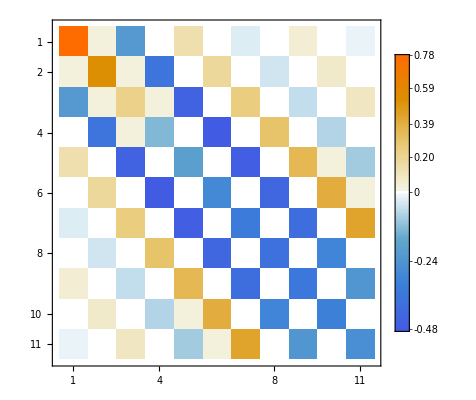

```mathematica
MatrixPlot[IntD[0.7], PlotLegends -> True] (*test*)
```

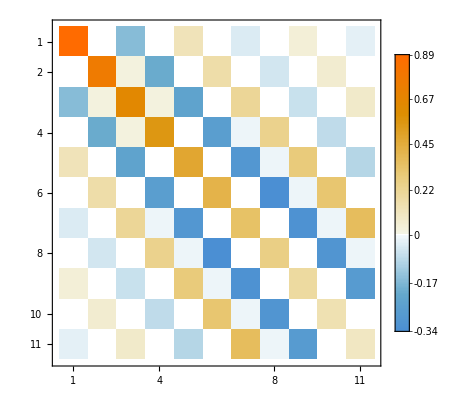

```mathematica
MatrixPlot[IntDr[0.7], PlotLegends -> True] (*test*)
```

```mathematica
U12= IntU[omega[1],omega[2], (1/g21) //N];
```

```mathematica
MatrixPlot[U12]
```

```mathematica
U23 = IntU[omega[2],omega[3], (1/g23) //N];
```

```mathematica
U34 = IntU[omega[3],omega[4], (1/g34) //N];
```

Power::indet: Indeterminate expression (0.+0. ⅈ)^0 encountered.

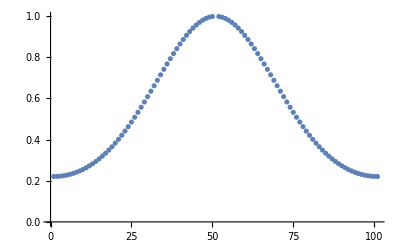

```mathematica
ListPlot[Table[Abs[Drw[15,15, 0.2, θ]]^2,{θ,0, Pi, Pi/100}]]
```

```mathematica
0
```

```mathematica
U12= IntU[omega[1],omega[2], (1/g21) //N];
U23 = IntU[omega[2],omega[3], (1/g23) //N];
U35 = IntU[omega[3],omega[5], (1/g35) //N];
U41 = IntU[omega[4],omega[1], (1/g41) //N];
U64 = IntU[omega[6],omega[4], (1/g64) //N];
U51 = IntU[omega[5],omega[1], (1/g51) //N];
U65 = IntU[omega[6],omega[5], (1/g65) //N];
U75 = IntU[omega[7],omega[5], (1/g75) //N];
U27 = IntU[omega[2],omega[7], (1/g27) //N];
U26 = IntU[omega[2],omega[6], (1/g26) //N];
U34 = IntU[omega[3],omega[4], (1/g34) //N];
```

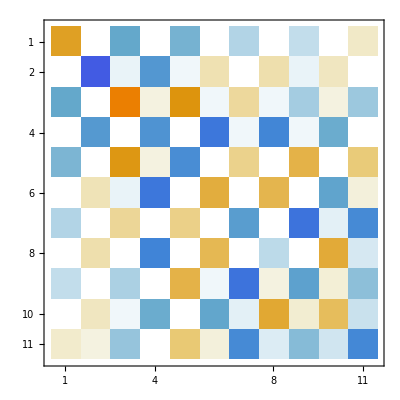
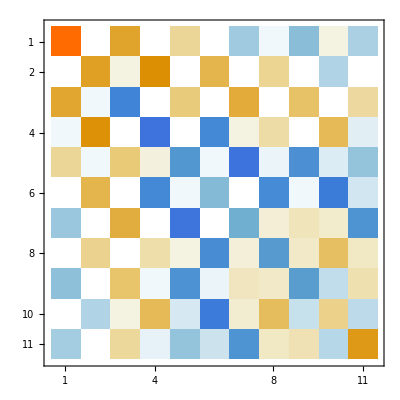
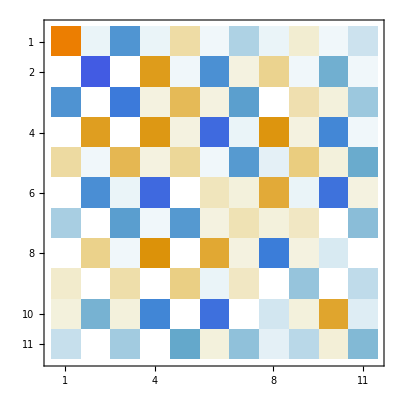
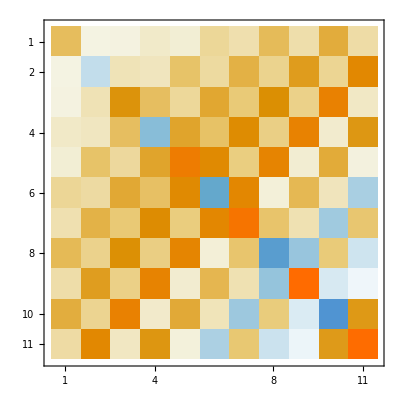
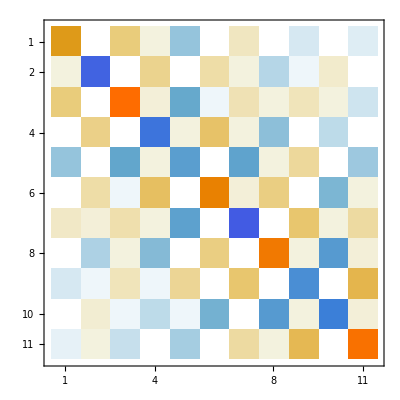
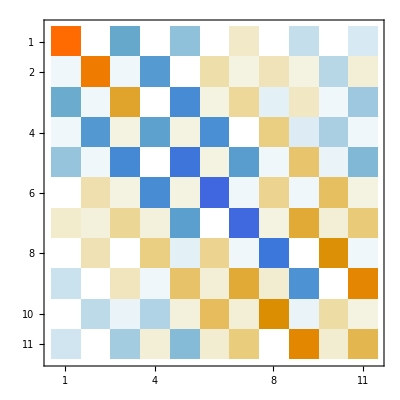
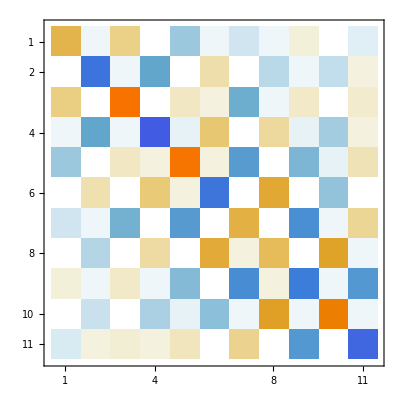
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{MatrixPlot[U12],MatrixPlot[U23],MatrixPlot[U35],MatrixPlot[U41],MatrixPlot[U64],MatrixPlot[U51],MatrixPlot[U65],MatrixPlot[U75],MatrixPlot[U27],MatrixPlot[U26],MatrixPlot[U34]}
```

```mathematica
(*omegas = {93404.36151476773,58312.21388517295,52564.18722654877,96487.56959133178,149378.74074871602,114323.656390064,134446.8575802304};*)
```

```mathematica
D12 = IntD[eta[1]];
D21 = IntDr[eta[1]];
D23 = IntDr [eta[2]];
D35 = IntDr[eta[3]];
D41 = IntDr[eta[4]];
D64 = IntDr[eta[5]];
D51 = IntDr[eta[6]];
D65 = IntDr[eta[7]];
D75 = IntDr[eta[8]];
D27 = IntDr[eta[9]];
{{D26 = IntDr[eta[10]];}, {D34 = IntDr[eta[11]];}}
```

{{Null},{Null}}

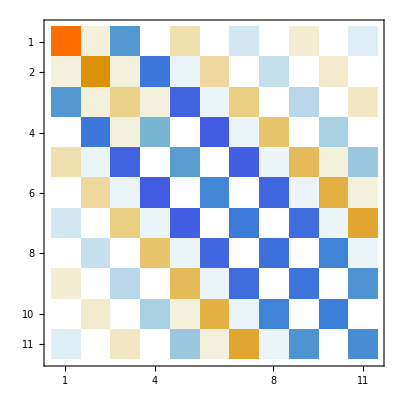
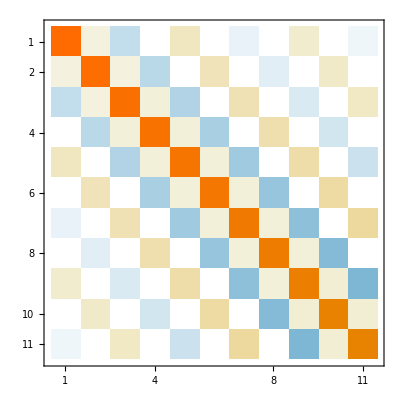
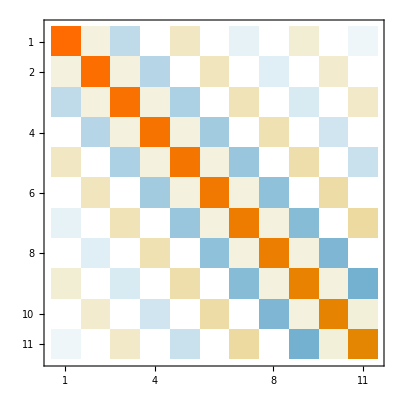
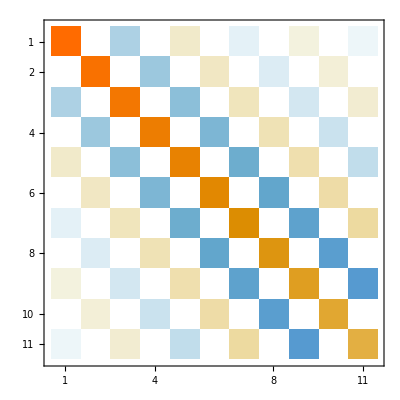
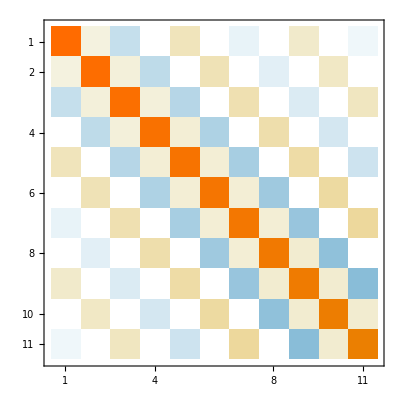
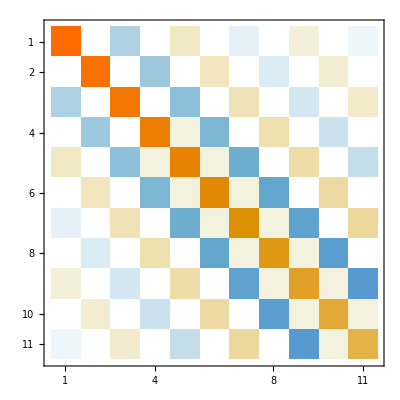
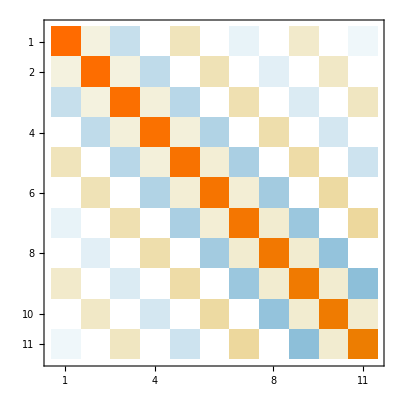
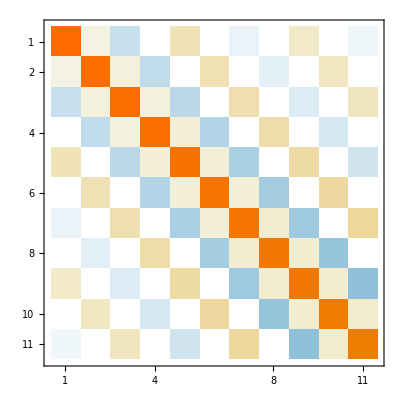

```mathematica
{MatrixPlot[D12],MatrixPlot[D23],MatrixPlot[D35],MatrixPlot[D41],MatrixPlot[D64],MatrixPlot[D51],MatrixPlot[D65],MatrixPlot[D75],MatrixPlot[D27],MatrixPlot[D26],MatrixPlot[D34]}
```

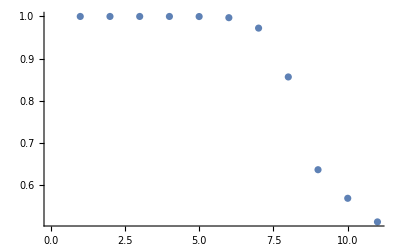

```mathematica
ListPlot[Table[Total[Table[Abs[D12[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

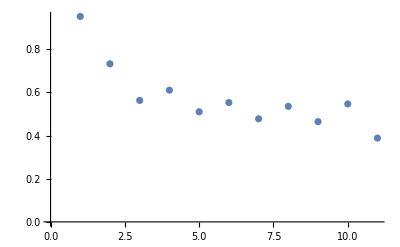

```mathematica
ListPlot[Table[Total[Table[Abs[(D21.D21.D21.D21.D21)[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

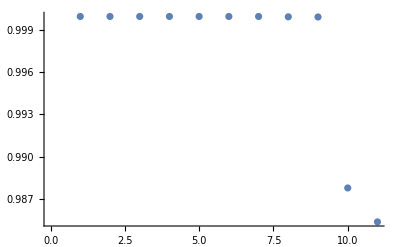

```mathematica
ListPlot[Table[Total[Table[Abs[U34[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

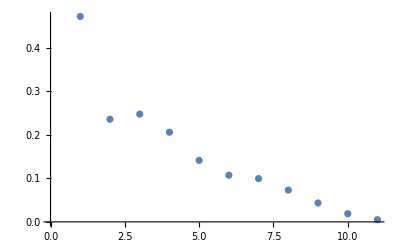

```mathematica
ListPlot[Table[Total[Table[Abs[PathA[[l,j+1]]]^2,{j,0,nmax}]],{l,1,nmax+1}]]
```

```mathematica
pathA = D41.U34.D34.U23.D23.U12.D12; (*7p3/2 -> 7s1/2 -> 6p1/2-> 6s1/2*)
pathB = D51.U35.D35.U23.D23.U12.D12;(*7p3/2 -> 7s1/2 -> 6p3/2-> 6s1/2*)
pathC = D51.U65.D65.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p3/2-> 6s1/2*)
pathD = D41.U64.D64.U26.D26.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathE = D51.U75.D75.U27.D27.U12.D12;(*7p3/2 -> 5d3/2 -> 6p1/2-> 6s1/2*)
pathF = D21.U12.D12;

paths ={pathA, pathB, pathC, pathD, pathE, pathF};

PathA = Table[Abs[pathA[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathB = Table[Abs[pathB[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathC = Table[Abs[pathC[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathD = Table[Abs[pathD[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathE = Table[Abs[pathE[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
PathF = Table[Abs[pathF[[i+1,j+1]]]^2,{i,0,nmax}, {j,0,nmax}];
Paths ={PathA, PathB, PathC, PathD, PathE, PathF};
```

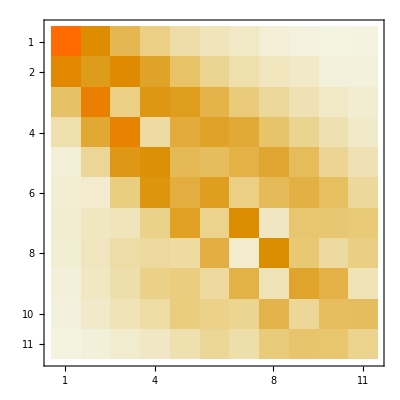
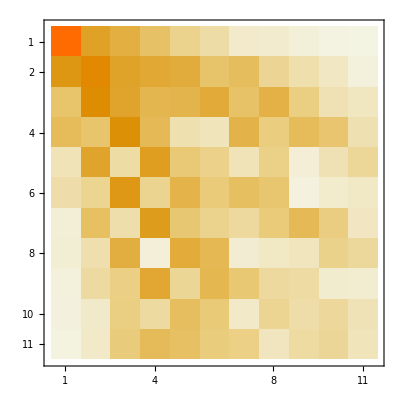
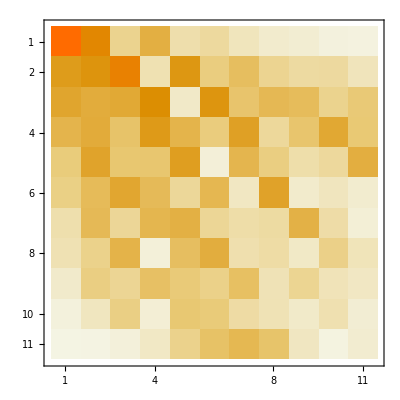
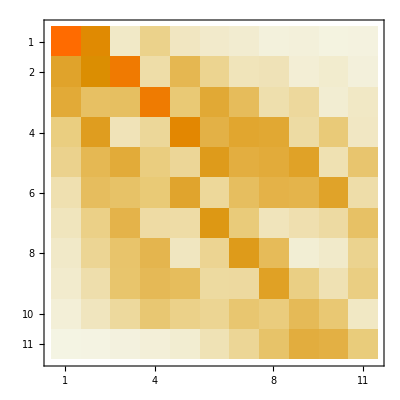
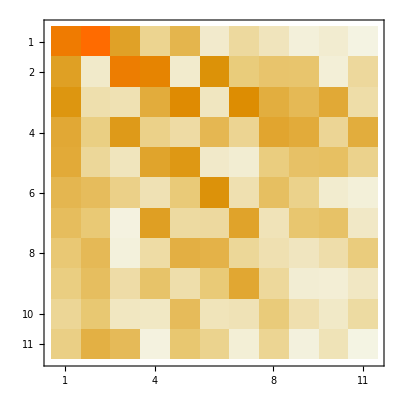
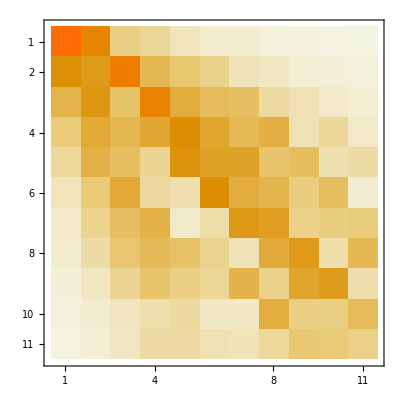

```mathematica
{MatrixPlot[PathA],MatrixPlot[PathB],MatrixPlot[PathC],MatrixPlot[PathD],MatrixPlot[PathE],MatrixPlot[PathF]}
```

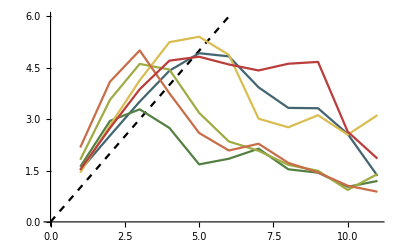

```mathematica
plotPath[pa_]:=ListPlot[Table[Sum[Paths[[pa]][[r,All]][[ra]] ra,{ra,1,nmax+1}],{r,1,Length[Paths[[pa]][[1,All]]]}],PlotStyle -> ColorData["DarkRainbow"][pa/6],Joined -> True]
Show[{Plot[x,{x,0,6}, PlotStyle -> Directive[Black, Dashed]],Table[plotPath[p],{p,1,6}]},PlotRange-> All]
```

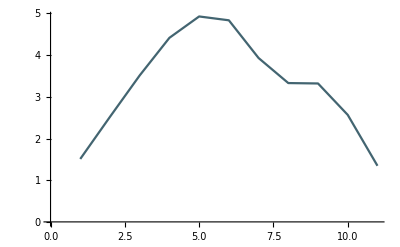
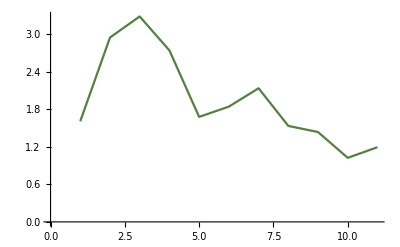
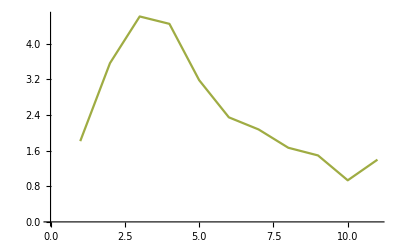
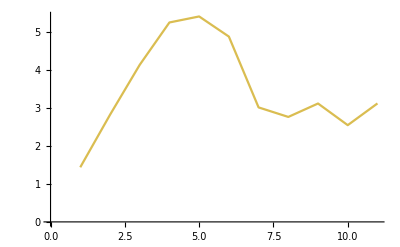
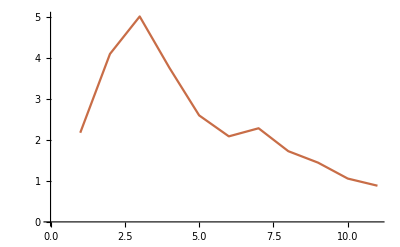
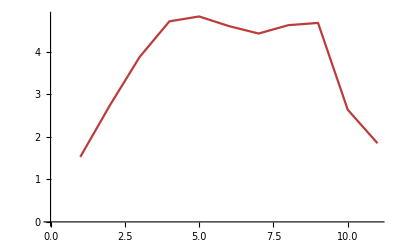

```mathematica
Table[plotPath[p],{p,1,6}]
```

```mathematica
PathTot = 0.201004*PathA +0.3678 PathB +0.001969 PathC + 0.016289PathD + 0.154494PathE + 0.258427 PathF
```

{{0.600925,0.26184,0.0733526,0.0285515,0.0193615,0.00610245,0.00396204,0.00237763,0.000658622,0.000623085,0.000112302},{0.208687,0.206173,0.268852,0.13034,0.0607378,0.0513059,0.0249369,0.0132598,0.010018,0.00259243,0.0025601},{0.0744946,0.231133,0.069506,0.175241,0.118157,0.078453,0.0695918,0.0458498,0.0204572,0.0174456,0.00421277},{0.0451106,0.0788561,0.20128,0.0557858,0.0970522,0.0767483,0.0771524,0.0636614,0.0375591,0.023497,0.0172823},{0.02124,0.0787167,0.0659824,0.127825,0.100676,0.0603569,0.0609841,0.0594113,0.0423619,0.016094,0.0138617},{0.01556,0.0278371,0.106913,0.0561018,0.0562708,0.131487,0.0502037,0.0593205,0.0360707,0.0353575,0.00489453},{0.0093169,0.0297853,0.0245457,0.106353,0.0474838,0.0189241,0.120718,0.0503511,0.0416258,0.0347322,0.0215071},{0.00675977,0.0162603,0.0503916,0.0255665,0.0664693,0.0595303,0.00858183,0.083755,0.0555419,0.013882,0.035583},{0.00495854,0.0141994,0.0182267,0.0684731,0.0225351,0.0330434,0.0724338,0.0186728,0.0699734,0.0654804,0.00605507},{0.00275511,0.00742159,0.0125613,0.0110463,0.0338258,0.016817,0.00799089,0.059232,0.0191013,0.0296027,0.037541},{0.00397054,0.0137264,0.0193006,0.0224436,0.0258868,0.0183698,0.0121788,0.0158446,0.0304043,0.0301503,0.0155786}}

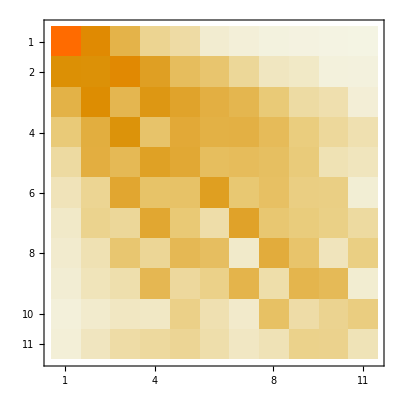

```mathematica
MatrixPlot[PathTot]
```

```mathematica
paths ={PathA, PathB, PathC, PathD, PathE, PathF, PathTot};
```

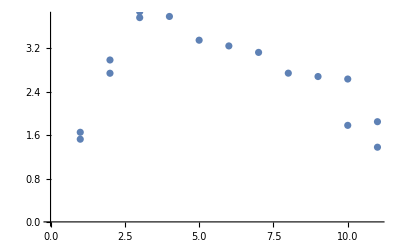

```mathematica
Show[{plotpath[7],plotpath[6],}]
```